## Convex sets and functions

A set C is affine if for x, y in C then θ x + (1 - θ) y is also in C

A set C is convex if the above holds with θ ≥ 0

A function f is convex if f[θ x + (1- θ) y] ≤ θ f[x]+(1-y)f[y] for θ ≥ 0 and all x, y in the domain of f

The epigraph of a function is the set {x, t} such that x is in the domain of f and f[x] ≤ t

## A Big thing

The optimization problem

minimize f_o[x]
subject to f_i[x] ≤ 0,  i=1, ...m
		h_j[x] = 0, j=1, ...p

is a convex optimization problem if f_i[x] are convex and h_j[x] are affine (h_j[x] = a_j.x + b_j)

For a convex optimization problem, a local minimum is also a global minimum!

Note the problem has the equivalent expression :

minimize t
subject to f_o[x] - t ≤ 0
		f_i[x] ≤ 0, i=1,...m
		a_j x + b_j = 0, j=1, ...p

So both the objective function and any equality constraints are linear

## Convex Proper Cones

A cone is a set k such that if x ∈ k, θ x ∈ k where θ≥0.

A convex cone is a cone that also satisfies θ_1 x_1 + θ_2 x_2 ∈ k for θ_1 ≥ 0, θ_2≥0

A proper cone has non-empty interior and is pointed (x ∈ k and -x ∈ k ⟺x=0

```mathematica
RegionPlot3D[Sqrt[x^2+y^2] ≤z, {x,-1,1},{y,-1,1},{z,0,1}, Mesh->None, PlotPoints->50]
```

-Graphics3D-

```mathematica
RegionPlot3D[Sqrt[x^2]≤z,{x,-1,1},{y,-1,1},{z,0,1}, Mesh->None, PlotPoints->50]
```

-Graphics3D-

## Some Common Cones 7:37

NonNegativeCone[n] 	: 	x ∈ ℝ^n such that x_i≥0

NormCone[n] 			:	 {t, x} ∈ ℝ  x ℝ^n such that Norm[x] ≤ t

SemiDefiniteCone[n]	:	 symmetric positive definite n x n matrices

ExponentialCone[ ]	: 	{x,y,z} ∈ ℝ^3 such that y ⅇ^(x/y)≤z

PowerCone[α]			:	 {x,y,z} ∈ ℝ^3 such that x^α y^(1-α)≥z, x≥0, y≥0

### NonNegativeCone

```mathematica
RegionPlot3D[{x,y,z}\[VectorGreaterEqual]0,{x,0,1},{y,0,1},{z,0,1},Mesh->None]
```

-Graphics3D-

### NormCone

```mathematica
RegionPlot3D[Norm[{x,y}]\[VectorLessEqual]z,{x,-1,1},{y,-1,1},{z,0,1},Mesh->None]
```

-Graphics3D-

### SemiDefiniteCone

### ExponentialCone

```mathematica
Quiet@RegionPlot3D[y* ⅇ^(x/y)\[VectorLessEqual]z,{x,-1,1},{y,-1,1},{z,-1,1},Mesh->None]
```

-Graphics3D-

### PowerCone

```mathematica
Quiet@RegionPlot3D[x^0.6*y^(1-0.6)\[VectorGreaterEqual]z,{x,0,1},{y,0,1},{z,-1,1},Mesh->None]
```

-Graphics3D-

## Generalized Inequalities

Let K be a proper cone. Then one can define a partial order based on k:

x (\[VectorLessEqual])_k y ⟺ y-x ∈ k

x (\[VectorGreaterEqual])_k y ⟺ x-y ∈ k

```mathematica
FullForm[{x(\[VectorLessEqual])_k y, x(\[VectorGreaterEqual])_k y}]
```

List[VectorLessEqual[List[x,y],k],VectorGreaterEqual[List[x,y],k]]

Two really frequent and distinguishable causes can be given without the cone:

Vectors of length n : NonNegativeCone[n]

n x n matrices : SemidefiniteCone[n]

These evaluates if x and y are numerical:

```mathematica
rx = RandomReal[1,{100}];
rx \[VectorGreaterEqual]0
```

True

Zero is a special case -- normally requires consistent vector on both sides

```mathematica
mx=KroneckerProduct[rx,rx];
mx\[VectorGreaterEqual]0
```

True

```mathematica
Min[Eigenvalues[mx]]
```

-1.85182×10^-15

```mathematica
PositiveSemidefiniteMatrixQ[mx]
```

True

## Conic Optimization

minimize c.x

subject to a_1.x + b_1(\[VectorGreaterEqual])_k_1 0
...
a_n.x + b_n(\[VectorGreaterEqual])_k_n 0
a_0.x + b_o=0
where k_1,..., k_n are proper cones, x is a vector of length n, a_i are m_i x n matrices, and b_i are vectors of length m_i

Linear optimization (programming) is a special case of this:

minimize c.x

subject to a_i .x + b_i\[VectorGreaterEqual]0
a_o. x + b_o=0
the cone is the non-negative cone

Another way to express the conic problem is

minimize c.x
subject to a_1.x + b_1∈k_1
...
a_n.x + b_n∈k_n
a_o.x + b_o=0

## Cone Transformation

Consider the set of x∈ℝ^n such that a.x +b ∈k (or a.x (\[VectorGreaterEqual])_k-b) for some cone k

In our development framework (for lack of a better name) we are denoting a canonical form of this by ConeTransformation[k, {a,b}]

```mathematica
a={{1,0},{0,1},{-1,-2}};
```

```mathematica
b={0,0,2};
```

```mathematica
set=ConeTransformation[NonNegativeCone[3],{a,b}];
```

```mathematica
set=VectorGreaterEqual[]
```

```mathematica
pl=RegionPlot[{x,y}∈set,{x,0,2},{y,0,1},PlotStyle->Opacity[.5],AspectRatio->Automatic]
```

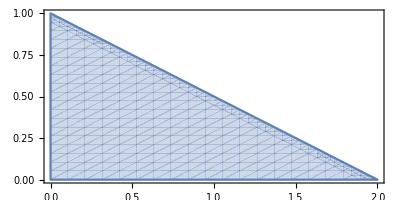

```mathematica
Quiet@RegionPlot[a.{x,y}+b\[VectorGreaterEqual]0,{x,0,2},{y,0,1},AspectRatio->Automatic]
```

## ConicOptimization Function/

```mathematica
c=-{1,1};
xmin=ConicOptimization[c,set]
```

{-1,-1}